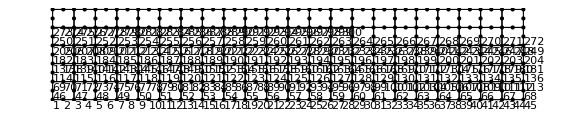

```mathematica
GenerateGraphics[nodes_,topology_,order_]:=Block[{meshvis,nodevis,v},If[order==1,v={1,2,3,4},v={1,5,2,6,3,7,4,8}];
meshvis=Graphics[{FaceForm[],EdgeForm[Black],GraphicsComplex[nodes,Polygon[topology[[All,v]]]]}];
(*nodevis=Graphics[{MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nodes],{Blue,Point[nodes]}}];*)
nodevis=Graphics[{MapIndexed[Style[Text[#2[[1]],#1,{-1.8,1.8}],FontSize->9]&,nodes],{PointSize[Large],Black,Point[nodes]}}];
{meshvis,nodevis}
];
meshnodes=Import["D:\stochasticfem\SFEM\SFEM\meshcoords.txt","Table"];
meshtopology=Import["D:\stochasticfem\SFEM\SFEM\meshtopology.txt","Table"];
order=2;
{meshvis,nodevis}=GenerateGraphics[meshnodes,meshtopology+1,order];(*Generates graphics to visualize mesh*)
Show[meshvis,nodevis,AspectRatio->Automatic,ImageSize->Large]
```

```mathematica
plot={};
For[i=0,i<5,i++,
s="D:\\stochasticfem\\SFEM\\SFEM\\eigenfunction";
randomfield=Import[StringJoin[s,ToString[i]<>".txt"],"Table"];
AppendTo[plot,ListContourPlot[randomfield,AspectRatio->Automatic,ImageSize->Large]];

];
plot
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
s="D:\\stochasticfem\\SFEM\\SFEM\\VARERROOOO.txt";
randomfield=Import[s,"Table"];
ListContourPlot[randomfield,AspectRatio->Automatic,ImageSize->Large,PlotLegends->Automatic]
```

-Graphics-

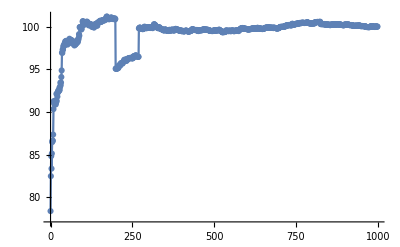

```mathematica
s="D:\\stochasticfem\\SFEM\\SFEM\\saidafina.txt";
meanvec=Abs[Import[s,"Table"]];
ListLinePlot[meanvec,PlotRange->All,PlotMarkers->Automatic]
```

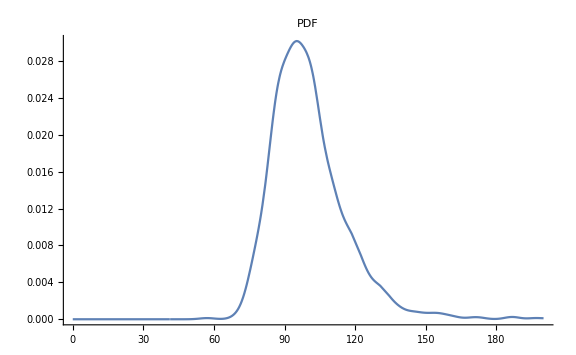
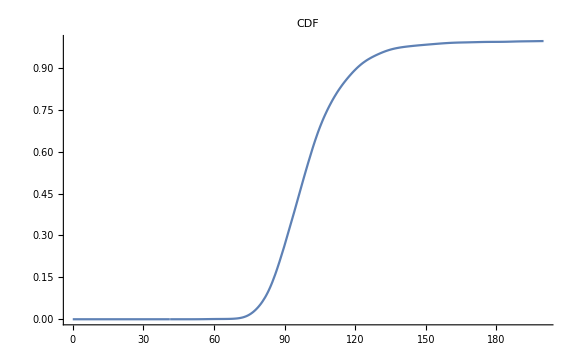

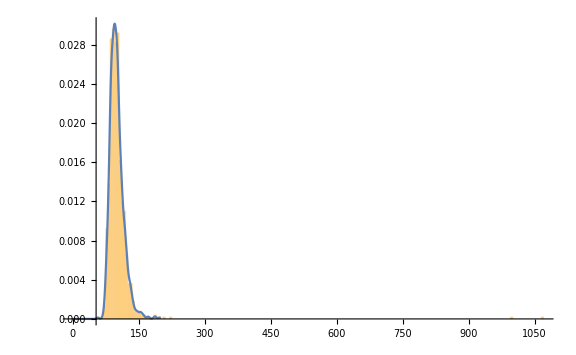

102.378

44.8614

0.438192

```mathematica
s="D:\\stochasticfem\\SFEM\\SFEM\\saidafina2.txt";
l2=Flatten[Abs[Import[s,"Table"]]];
𝒟=SmoothKernelDistribution[l2];
Table[Plot[f[𝒟,x],{x,0,200},PlotLabel->f,PlotRange->All,ImageSize->Large],{f,{PDF,CDF}}]
Show[Histogram[l2,Automatic,"PDF"],Plot[PDF[𝒟,x],{x,0,200}],ImageSize->Large,PlotRange->All]
Mean[l2]
StandardDeviation[l2]
StandardDeviation[l2]/Mean[l2]
```